# JIDHUN PP | BSc(Hons) Computer Science| 20211419|Practical-1

## Plotting Of First Order Solution Of Family Of Differential Equation Solving first Order Ordinary Differential Equation : QUES 1 : Solve First Order Differential Equation y'[x] - 6 x^2 - 2 x - 3 = 0. SOL :

```mathematica
DSolve[y'[x]-6x^2-2x-3==0,y[x],x]
```

{{y[x]→3 x+x^2+2 x^3+C[1]}}

### QUES 2 : Solve First Order Differential Equation y’[x] -3 x ^ 2 - 2 x - 1 = 0. SOL :

```mathematica
DSolve[y'[x]-3x^2-2x-1==0,y[x],x]
```

{{y[x]→x+x^2+x^3+C[1]}}

### QUES 2 : Solve First Order Differential Equation y'[x] - 3 Exp[x - y] - x^2*Exp[-y] = 0 SOL :

```mathematica
DSolve[y'[x]-3Exp[x-y[x]]-x^2*Exp[-y[x]]==0,y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→Log[3 ⅇ^x+x^3/3+C[1]]}}

### Plotting of solutions of first order differential equation: QUES 1: Solve the first order differential equation y ‘ [x] - 1 - x - y [x] - x *y [x] = 0 and plot its three solutions SOL :

```mathematica
Sol=DSolve[y'[x]-1-x-y[x]-x*y[x]==0,y[x],x]
```

{{y[x]→-ⅇ^(x+x^2/2-1/2 x (2+x))+ⅇ^(x+x^2/2) C[1]}}

```mathematica
Sol1=y[x]/.Sol[[1]]/.{C[1]->-10}
```

-10 ⅇ^(x+x^2/2)-ⅇ^(x+x^2/2-1/2 x (2+x))

```mathematica
Sol2=y[x]/.Sol[[1]]/.{C[1]->-0}
```

-ⅇ^(x+x^2/2-1/2 x (2+x))

```mathematica
Sol3=y[x]/.Sol[[1]]/.{C[1]->10}
```

10 ⅇ^(x+x^2/2)-ⅇ^(x+x^2/2-1/2 x (2+x))

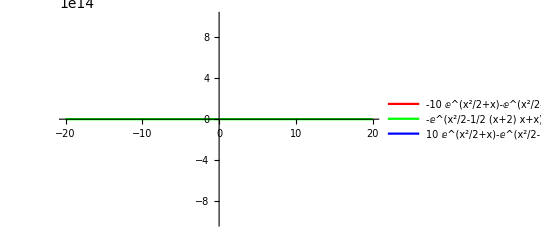

```mathematica
Plot[{Sol1,Sol2,Sol3},{x,-20,20},
PlotStyle->{{Red},{Green},{Blue}},
PlotLegends->{Sol1,Sol2,Sol3}]
```

### QUES 2: Solve the first order differential equation y ‘[x]-Exp[x-y] - x^2*Exp[ -y] = 0 and plot its three solutions SOL :

```mathematica
Sol=DSolve[y'[x]-Exp[x-y[x]]-x^2*Exp[-y[x]]==0,y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→Log[ⅇ^x+x^3/3+C[1]]}}

```mathematica
Sol1=y[x]/.Sol[[1]]/.{C[1]->10}
```

Log[10+ⅇ^x+x^3/3]

```mathematica
Sol2=y[x]/.Sol[[1]]/.{C[1]->0}
```

Log[ⅇ^x+x^3/3]

```mathematica
Sol3=y[x]/.Sol[[1]]/.{C[1]->-10}
```

Log[-10+ⅇ^x+x^3/3]

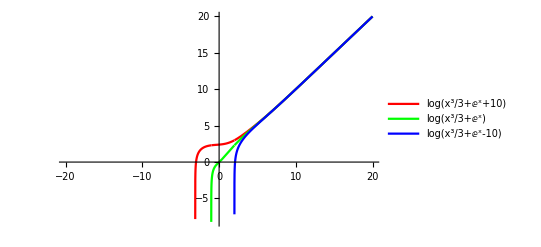

```mathematica
Plot[{Sol1,Sol2,Sol3},{x,-20,20},
PlotStyle->{{Red},{Green},{Blue}},
PlotLegends->{Sol1,Sol2,Sol3}]
```

### QUES 3 : Solve the first order differential equation y ‘[x]*Sin[Pi*x]-y[x]*Cos[Pi*x]=0 and plot its three solutions SOL :

```mathematica
Sol=DSolve[y'[x]*Sin[Pi*x]-y[x]*Cos[Pi*x]==0,y[x],x]
```

{{y[x]→C[1] Sin[π x]^(1/π)}}

```mathematica
Sol1=y[x]/.Sol[[1]]/.{C[1]->10}
```

10 Sin[π x]^(1/π)

```mathematica
Sol2=y[x]/.Sol[[1]]/.{C[1]->5}
```

5 Sin[π x]^(1/π)

```mathematica
Sol3=y[x]/.Sol[[1]]/.{C[1]->-10}
```

-10 Sin[π x]^(1/π)

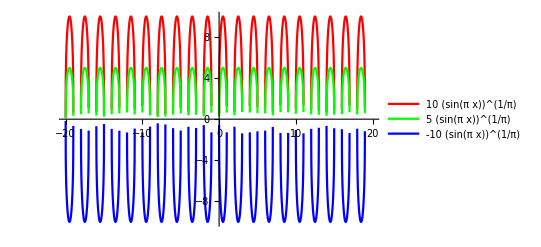

```mathematica
Plot[{Sol1,Sol2,Sol3},{x,-20,20},
PlotStyle->{{Red},{Green},{Blue}},
PlotLegends->{Sol1,Sol2,Sol3}]
```

### QUES 4 : Solve the first order differential equation y’[x]*(x-1)-2x*y[x]=0 and plot its three solutions SOL :

```mathematica
Sol=DSolve[y'[x]*(x-1)-2x*y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(2 (x+Log[-1+x])) C[1]}}

```mathematica
Sol1=y[x]/.Sol[[1]]/.{C[1]->10}
```

10 ⅇ^(2 (x+Log[-1+x]))

```mathematica
Sol2=y[x]/.Sol[[1]]/.{C[1]->1}
```

ⅇ^(2 (x+Log[-1+x]))

```mathematica
Sol3=y[x]/.Sol[[1]]/.{C[1]->-10}
```

-10 ⅇ^(2 (x+Log[-1+x]))

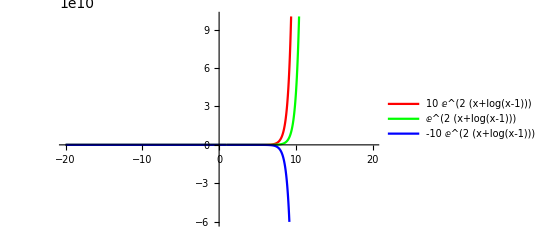

```mathematica
Plot[{Sol1,Sol2,Sol3},{x,-20,20},
PlotStyle->{{Red},{Green},{Blue}},
PlotLegends->{Sol1,Sol2,Sol3}]
```